```mathematica
(*Problem 3.28*)
g[t_]:=Piecewise[{{-1, -π/ω[T]<=t<=0}, {1, 0<=t<=π/ω[T]}}]
```

```mathematica
ω[T_]:=(2π)/T
```

```mathematica
T=2π; (*This is the period when ω=1*)
```

```mathematica
(*Telling Mathematica that n is an integers to simplify the integration*)
```

```mathematica
$Assumptions = n ∈ Integers;
```

```mathematica
1/π* ∫_(-π/ω[2π])^(π/ω[2π]) g[t]ⅆt (*integrating to obtain A0*)
```

0

```mathematica
a00=0;
```

```mathematica
ω[T]/π* ∫_(-π/ω[T])^(π/ω[T]) g[t]*Cos[n*ω[T]*t]ⅆt (*integrating to obtain An*)
```

0

```mathematica
ann[n_]:=0;
```

```mathematica
ω[T]/π* ∫_(-π/ω[T])^(π/ω[T]) g[t]*Sin[n*ω[T]*t]ⅆt (*integrating to obtain Bn*)
```

-(2 (-1+(-1)^n))/(n π)

```mathematica
bn[n_]:=-(2 (-1+(-1)^n))/(n π);
```

```mathematica
(*Defining Fourier series expansion*)FouriSeri[k_,T_,t_]:=∑_(n=1)^k (bn[n]*Sin[n*ω[T]*t]+ann[n]*Cos[n*ω[t]*t])+a00/2
```

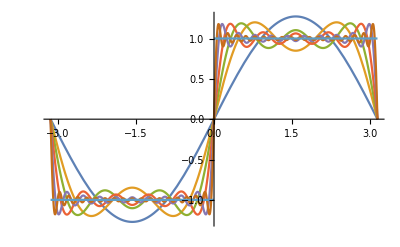

```mathematica
(*Plotting Multiple terms of fourier series expansion to show how it is approaching g[t] as the number of terms increases,from 2 to 35 *)Plot[{ FouriSeri[2,2*π,t],FouriSeri[4,2*π,t],FouriSeri[6,2*π,t],FouriSeri[10,2*π,t],FouriSeri[20,2*π,t],FouriSeri[35,2*π,t],g[t]},{t,-π,π}]
```

```mathematica
(* a nice way to play with the valuse of n *)
Manipulate[Plot[{FouriSeri[n,2*π,t],g[t]},{t,-π,π}, PlotStyle->{Blue, Green}],{n,1,40,1}]
```

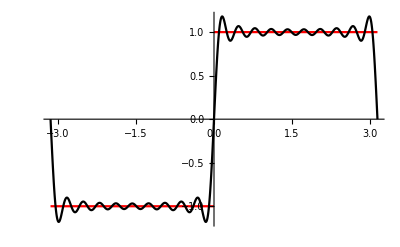

```mathematica
(* ALso this can be done using mathematica's library with a single command as shown below*)
Mathe=FourierSeries[g[t],t,20];
Plot[{g[t],Mathe}, {t, -π,π}, PlotStyle->{Red, Black}]
```